```mathematica
data=ResourceObject["CIFAR-100"];
testData=ResourceData[data,"TestData"]
trainingData=ResourceData[data,"TrainingData"]
```

{-Graphics-→apple,-Graphics-→apple,-Graphics-→apple,-Graphics-→apple,-Graphics-→apple,-Graphics-→apple,-Graphics-→apple,-Graphics-→apple,-Graphics-→apple,-Graphics-→apple,-Graphics-→apple,-Graphics-→apple,-Graphics-→apple,-Graphics-→apple,-Graphics-→apple,-Graphics-→apple,-Graphics-→apple,-Graphics-→apple,-Graphics-→apple,-Graphics-→apple,-Graphics-→apple,-Graphics-→apple,-Graphics-→apple,-Graphics-→apple,-Graphics-→apple,-Graphics-→apple,-Graphics-→apple,-Graphics-→apple,-Graphics-→apple,-Graphics-→apple,9940,-Graphics-→worm,-Graphics-→worm,-Graphics-→worm,-Graphics-→worm,-Graphics-→worm,-Graphics-→worm,-Graphics-→worm,-Graphics-→worm,-Graphics-→worm,-Graphics-→worm,-Graphics-→worm,-Graphics-→worm,-Graphics-→worm,-Graphics-→worm,-Graphics-→worm,-Graphics-→worm,-Graphics-→worm,-Graphics-→worm,-Graphics-→worm,-Graphics-→worm,-Graphics-→worm,-Graphics-→worm,-Graphics-→worm,-Graphics-→worm,-Graphics-→worm,-Graphics-→worm,-Graphics-→worm,-Graphics-→worm,-Graphics-→worm,-Graphics-→worm}
 |  |  |  |

{-Graphics-→apple,-Graphics-→apple,-Graphics-→apple,-Graphics-→apple,-Graphics-→apple,-Graphics-→apple,-Graphics-→apple,-Graphics-→apple,-Graphics-→apple,-Graphics-→apple,-Graphics-→apple,-Graphics-→apple,-Graphics-→apple,-Graphics-→apple,-Graphics-→apple,-Graphics-→apple,-Graphics-→apple,-Graphics-→apple,-Graphics-→apple,-Graphics-→apple,-Graphics-→apple,-Graphics-→apple,-Graphics-→apple,-Graphics-→apple,-Graphics-→apple,-Graphics-→apple,-Graphics-→apple,-Graphics-→apple,-Graphics-→apple,-Graphics-→apple,49940,-Graphics-→worm,-Graphics-→worm,-Graphics-→worm,-Graphics-→worm,-Graphics-→worm,-Graphics-→worm,-Graphics-→worm,-Graphics-→worm,-Graphics-→worm,-Graphics-→worm,-Graphics-→worm,-Graphics-→worm,-Graphics-→worm,-Graphics-→worm,-Graphics-→worm,-Graphics-→worm,-Graphics-→worm,-Graphics-→worm,-Graphics-→worm,-Graphics-→worm,-Graphics-→worm,-Graphics-→worm,-Graphics-→worm,-Graphics-→worm,-Graphics-→worm,-Graphics-→worm,-Graphics-→worm,-Graphics-→worm,-Graphics-→worm,-Graphics-→worm}
 |  |  |  |

```mathematica
classes=Union@Values[trainingData]
```

{apple,aquarium fish,baby,bear,beaver,bed,bee,beetle,bicycle,bottle,bowl,boy,bridge,bus,butterfly,camel,can,castle,caterpillar,cattle,chair,chimpanzee,clock,cloud,cockroach,computer keyboard,couch,crab,crocodile,cup,dinosaur,dolphin,elephant,flatfish,forest,fox,girl,hamster,house,kangaroo,lamp,lawn-mower,leopard,lion,lizard,lobster,man,maple tree,motorcycle,mountain,mouse,mushroom,oak tree,orange,orchid,otter,palm tree,pear,pickup truck,pine tree,plain,plate,poppy,porcupine,possum,rabbit,raccoon,ray,road,rocket,rose,sea,seal,shark,shrew,skunk,skyscraper,snail,snake,spider,squirrel,streetcar,sunflower,sweet pepper,table,tank,telephone,television,tiger,tractor,train,trout,tulip,turtle,wardrobe,whale,willow tree,wolf,woman,worm}

```mathematica
lenet=NetChain[{ConvolutionLayer[20,5],Ramp,PoolingLayer[2,2],ConvolutionLayer[50,5],Ramp,PoolingLayer[2,2],FlattenLayer[],500,Ramp,100,SoftmaxLayer[]},"Output"->NetDecoder[{"Class",classes}],"Input"->NetEncoder[{"Image",{32,32}}]]
```

NetChain[]

```mathematica
trained=NetTrain[lenet,trainingData,MaxTrainingRounds->4]
```

NetChain[]

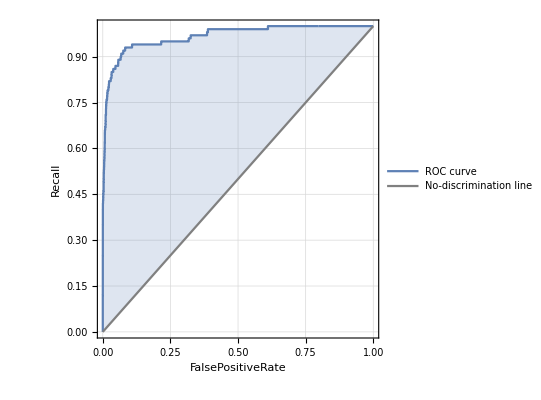
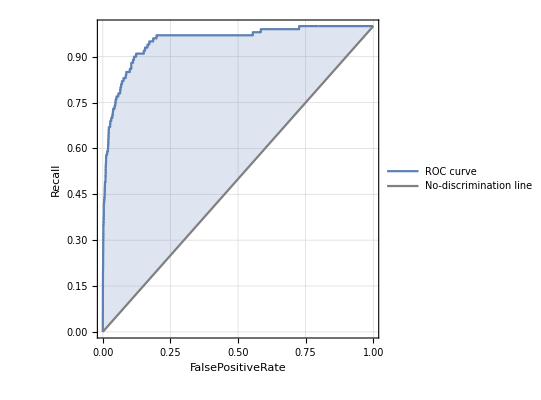
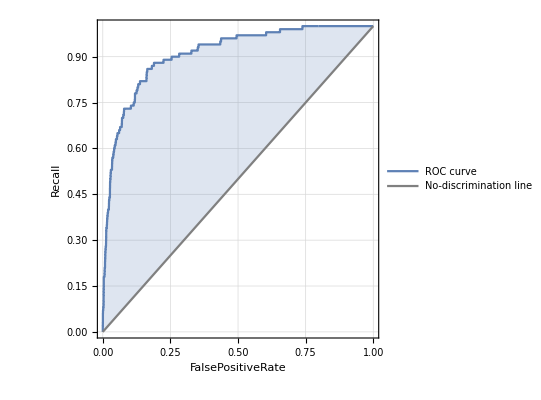
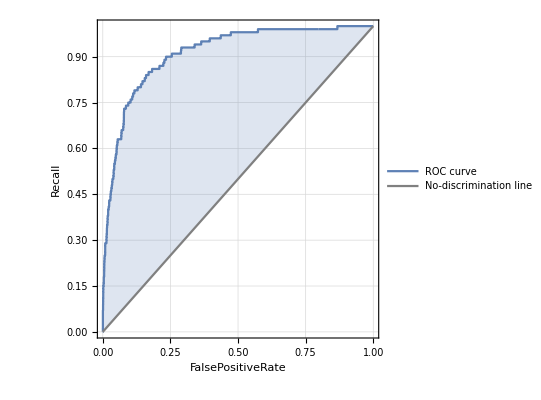
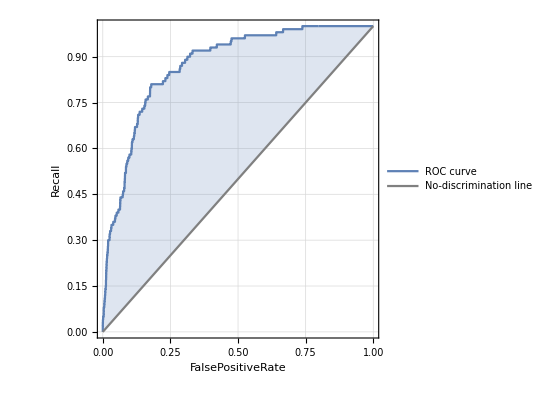
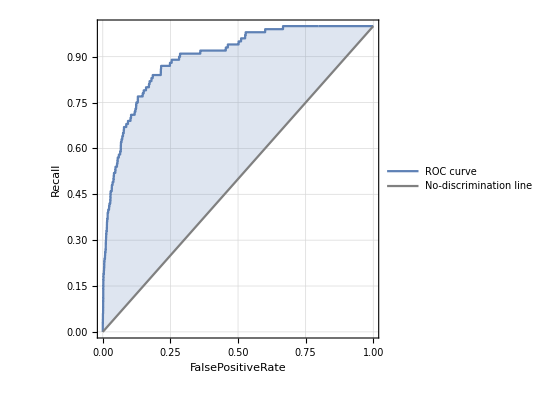
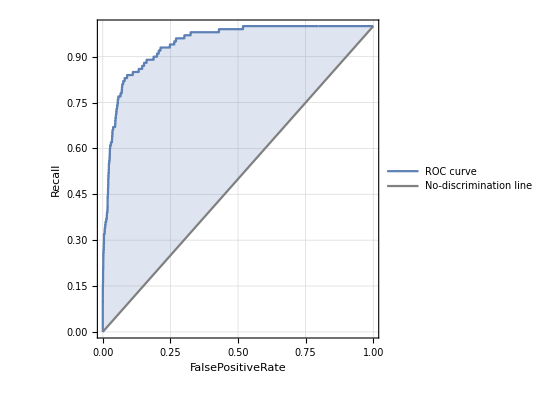
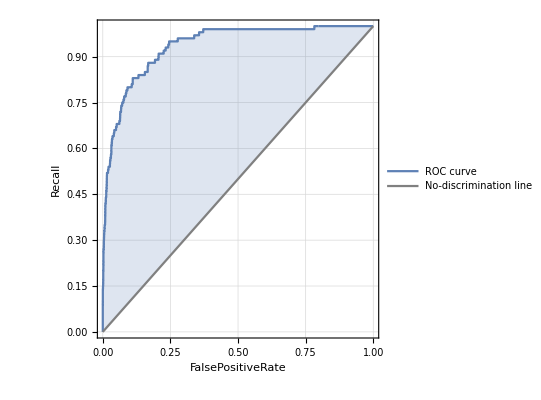
<|apple→-Graphics-,aquarium fish→-Graphics-,baby→-Graphics-,bear→-Graphics-,beaver→-Graphics-,bed→-Graphics-,bee→-Graphics-,beetle→-Graphics-,bicycle→-Graphics-,bottle→-Graphics-,bowl→-Graphics-,boy→-Graphics-,bridge→-Graphics-,bus→-Graphics-,butterfly→-Graphics-,camel→-Graphics-,can→-Graphics-,castle→-Graphics-,caterpillar→-Graphics-,cattle→-Graphics-,chair→-Graphics-,chimpanzee→-Graphics-,clock→-Graphics-,cloud→-Graphics-,cockroach→-Graphics-,computer keyboard→-Graphics-,couch→-Graphics-,crab→-Graphics-,crocodile→-Graphics-,cup→-Graphics-,dinosaur→-Graphics-,dolphin→-Graphics-,elephant→-Graphics-,flatfish→-Graphics-,forest→-Graphics-,fox→-Graphics-,girl→-Graphics-,hamster→-Graphics-,house→-Graphics-,kangaroo→-Graphics-,lamp→-Graphics-,lawn-mower→-Graphics-,leopard→-Graphics-,lion→-Graphics-,lizard→-Graphics-,lobster→-Graphics-,man→-Graphics-,maple tree→-Graphics-,motorcycle→-Graphics-,mountain→-Graphics-,mouse→-Graphics-,mushroom→-Graphics-,oak tree→-Graphics-,orange→-Graphics-,orchid→-Graphics-,otter→-Graphics-,palm tree→-Graphics-,pear→-Graphics-,pickup truck→-Graphics-,pine tree→-Graphics-,plain→-Graphics-,plate→-Graphics-,poppy→-Graphics-,porcupine→-Graphics-,possum→-Graphics-,rabbit→-Graphics-,raccoon→-Graphics-,ray→-Graphics-,road→-Graphics-,rocket→-Graphics-,rose→-Graphics-,sea→-Graphics-,seal→-Graphics-,shark→-Graphics-,shrew→-Graphics-,skunk→-Graphics-,skyscraper→-Graphics-,snail→-Graphics-,snake→-Graphics-,spider→-Graphics-,squirrel→-Graphics-,streetcar→-Graphics-,sunflower→-Graphics-,sweet pepper→-Graphics-,table→-Graphics-,tank→-Graphics-,telephone→-Graphics-,television→-Graphics-,tiger→-Graphics-,tractor→-Graphics-,train→-Graphics-,trout→-Graphics-,tulip→-Graphics-,turtle→-Graphics-,wardrobe→-Graphics-,whale→-Graphics-,willow tree→-Graphics-,wolf→-Graphics-,woman→-Graphics-,worm→-Graphics-|>

```mathematica
ClassifierMeasurements[trained, testData, "ROCCurve"]
```

```mathematica
ClassifierMeasurements[trained, testData, "Accuracy"]
```

0.3286

```mathematica
ClassifierMeasurements[trained, testData, "Precision"]
```

<|apple→0.408451,aquarium fish→0.444444,baby→0.151724,bear→0.256757,beaver→0.157895,bed→0.298701,bee→0.237288,beetle→0.391892,bicycle→0.429907,bottle→0.425743,bowl→0.219178,boy→0.148649,bridge→0.5,bus→0.529412,butterfly→0.31,camel→0.214286,can→0.337349,castle→0.576471,caterpillar→0.359551,cattle→0.25,chair→0.776316,chimpanzee→0.505155,clock→0.481481,cloud→0.430894,cockroach→0.371728,computer keyboard→0.56,couch→0.227586,crab→0.271739,crocodile→0.213333,cup→0.520833,dinosaur→0.397436,dolphin→0.571429,elephant→0.230769,flatfish→0.252336,forest→0.4,fox→0.333333,girl→0.25,hamster→0.167969,house→0.212121,kangaroo→0.141844,lamp→0.414286,lawn-mower→0.407895,leopard→0.592593,lion→0.201923,lizard→0.309091,lobster→0.166667,man→0.177305,maple tree→0.634146,motorcycle→0.42236,mountain→0.441558,mouse→0.1375,mushroom→0.612903,oak tree→0.557377,orange→0.468254,orchid→0.322222,otter→0.0689655,palm tree→0.560606,pear→0.306931,pickup truck→0.666667,pine tree→0.314286,plain→0.589552,plate→0.505618,poppy→0.5,porcupine→0.263566,possum→0.104895,rabbit→0.179487,raccoon→0.301887,ray→0.291667,road→0.816667,rocket→0.282787,rose→0.281081,sea→0.563107,seal→0.272727,shark→0.311111,shrew→0.156463,skunk→0.598039,skyscraper→0.674419,snail→0.166667,snake→0.201681,spider→0.284211,squirrel→0.150538,streetcar→0.333333,sunflower→0.636364,sweet pepper→0.242188,table→0.315789,tank→0.615385,telephone→0.471429,television→0.321429,tiger→0.45,tractor→0.37931,train→0.3,trout→0.440476,tulip→0.357143,turtle→0.168539,wardrobe→0.655556,whale→0.331126,willow tree→0.330435,wolf→0.251748,woman→0.133333,worm→0.269565|>

```mathematica
Values[%57]
```

{0.408451,0.444444,0.151724,0.256757,0.157895,0.298701,0.237288,0.391892,0.429907,0.425743,0.219178,0.148649,0.5,0.529412,0.31,0.214286,0.337349,0.576471,0.359551,0.25,0.776316,0.505155,0.481481,0.430894,0.371728,0.56,0.227586,0.271739,0.213333,0.520833,0.397436,0.571429,0.230769,0.252336,0.4,0.333333,0.25,0.167969,0.212121,0.141844,0.414286,0.407895,0.592593,0.201923,0.309091,0.166667,0.177305,0.634146,0.42236,0.441558,0.1375,0.612903,0.557377,0.468254,0.322222,0.0689655,0.560606,0.306931,0.666667,0.314286,0.589552,0.505618,0.5,0.263566,0.104895,0.179487,0.301887,0.291667,0.816667,0.282787,0.281081,0.563107,0.272727,0.311111,0.156463,0.598039,0.674419,0.166667,0.201681,0.284211,0.150538,0.333333,0.636364,0.242188,0.315789,0.615385,0.471429,0.321429,0.45,0.37931,0.3,0.440476,0.357143,0.168539,0.655556,0.331126,0.330435,0.251748,0.133333,0.269565}

```mathematica
StandardDeviation[%59]
```

0.163945

```mathematica
Mean[%59]
```

0.362468

```mathematica
ClassifierMeasurements[trained, testData, "Recall"]
```

<|apple→0.58,aquarium fish→0.44,baby→0.22,bear→0.19,beaver→0.15,bed→0.23,bee→0.42,beetle→0.29,bicycle→0.46,bottle→0.43,bowl→0.16,boy→0.11,bridge→0.16,bus→0.09,butterfly→0.31,camel→0.24,can→0.28,castle→0.49,caterpillar→0.32,cattle→0.12,chair→0.59,chimpanzee→0.49,clock→0.13,cloud→0.53,cockroach→0.71,computer keyboard→0.28,couch→0.33,crab→0.25,crocodile→0.32,cup→0.5,dinosaur→0.31,dolphin→0.2,elephant→0.39,flatfish→0.27,forest→0.32,fox→0.12,girl→0.03,hamster→0.43,house→0.21,kangaroo→0.2,lamp→0.29,lawn-mower→0.62,leopard→0.16,lion→0.42,lizard→0.17,lobster→0.22,man→0.25,maple tree→0.26,motorcycle→0.68,mountain→0.34,mouse→0.22,mushroom→0.19,oak tree→0.68,orange→0.59,orchid→0.58,otter→0.06,palm tree→0.37,pear→0.31,pickup truck→0.24,pine tree→0.22,plain→0.79,plate→0.45,poppy→0.42,porcupine→0.34,possum→0.15,rabbit→0.21,raccoon→0.16,ray→0.28,road→0.49,rocket→0.69,rose→0.52,sea→0.58,seal→0.03,shark→0.42,shrew→0.23,skunk→0.61,skyscraper→0.58,snail→0.2,snake→0.24,spider→0.27,squirrel→0.14,streetcar→0.18,sunflower→0.7,sweet pepper→0.31,table→0.06,tank→0.24,telephone→0.33,television→0.36,tiger→0.09,tractor→0.44,train→0.12,trout→0.37,tulip→0.1,turtle→0.15,wardrobe→0.59,whale→0.5,willow tree→0.38,wolf→0.36,woman→0.3,worm→0.31|>

```mathematica
Values[%61]
```

{0.58,0.44,0.22,0.19,0.15,0.23,0.42,0.29,0.46,0.43,0.16,0.11,0.16,0.09,0.31,0.24,0.28,0.49,0.32,0.12,0.59,0.49,0.13,0.53,0.71,0.28,0.33,0.25,0.32,0.5,0.31,0.2,0.39,0.27,0.32,0.12,0.03,0.43,0.21,0.2,0.29,0.62,0.16,0.42,0.17,0.22,0.25,0.26,0.68,0.34,0.22,0.19,0.68,0.59,0.58,0.06,0.37,0.31,0.24,0.22,0.79,0.45,0.42,0.34,0.15,0.21,0.16,0.28,0.49,0.69,0.52,0.58,0.03,0.42,0.23,0.61,0.58,0.2,0.24,0.27,0.14,0.18,0.7,0.31,0.06,0.24,0.33,0.36,0.09,0.44,0.12,0.37,0.1,0.15,0.59,0.5,0.38,0.36,0.3,0.31}

```mathematica
StandardDeviation[%62]
```

0.176452

```mathematica
Mean[%62]
```

0.3286